0.381418

0.9

{{y→InterpolatingFunction[…]}}

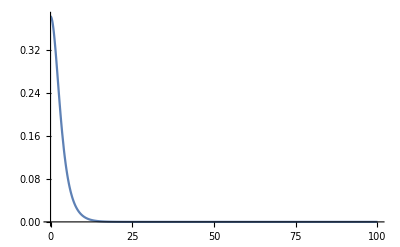

50

50000

1/1000

{0.0000153022,0.0000153089,0.0000153156,0.0000153223,0.0000153289,0.0000153356,0.0000153423,0.000015349,0.0000153557,0.0000153624,0.0000153691,0.0000153758,0.0000153825,0.0000153892,0.0000153959,0.0000154026,0.0000154093,0.000015416,0.0000154228,49962,0.0000154295,0.0000154228,0.000015416,0.0000154093,0.0000154026,0.0000153959,0.0000153892,0.0000153825,0.0000153758,0.0000153691,0.0000153624,0.0000153557,0.000015349,0.0000153423,0.0000153356,0.0000153289,0.0000153223,0.0000153156,0.0000153089}
 |  |  |  |

C:\Users\p_ana\Downloads\Research\Amin_Lab\Field_Evolution_Project\Polynomial Potential\1D_oscillon_profile.hdf5

```mathematica
y0 =0.3814175529434831
w=0.9
s=NDSolve[{y''[x]-4 y[x]^5+3 y[x]^3+(w^2-1)y[x]==0,y[0]==y0, y'[0]==0},y,{x,0,100}]
Plot[Evaluate[y[x]/.s],{x,0,100},PlotRange->All]
l = 50
n = 50000
dr = l/n
a=Flatten[Table[If[x<0,y[-x]/.s,y[x]/.s],{x,-l/2,l/2 - dr,dr}]]
Export["C:\\Users\\p_ana\\Downloads\\Research\\Amin_Lab\\Field_Evolution_Project\\Polynomial Potential\\1D_oscillon_profile.hdf5",a,"HDF5"]
```